### Adaptive search for doubling rules: close but no cigar

#### k = 4

```mathematica
dubevosk4 = ParallelTable[
SeedRandom[444210 + j];
AdaptiveCellularAutomaton[<|"Rule"->{0, 4, 1}, "Depth"->1000, 
"MutationFunction"->(RandomRuleMutation[#Rule, 1, "Symmetric"->True]&),
 "FitnessFunction"-> (-Total[Abs[Table[CenterArray[#, Max[Length[#],2i+2]&[#]] - CenterArray[Table[1, 2i+2], Max[Length[#],2i+2]]&[CellularAutomaton[#1, {Append[Table[1, i], 2], 0}, {{{60}}}]] , {i, 5}]], 2]&)|>], {j, 60}];
```

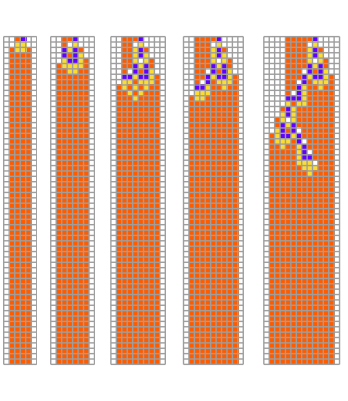

```mathematica
GraphicsRow[ArrayPlot[ArrayPad[#, 1]&/@#, ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]}, Mesh->True]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0}, 60], {i, 5}]&[MaximalBy[dubevosk4, #[[-1, "Fitness"]]&, 1][[1, -1]]]]
```

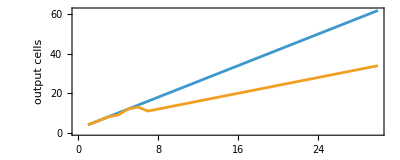

```mathematica
ListLinePlot[Join[{Table[ 2i+2, {i, 30}]}, Length/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0},{{{60}}}], {i, 30}]&/@ {MaximalBy[dubevosk4, #[[-1, "Fitness"]]&, 1][[1, -1]]}], PlotHighlighting->None, PlotStyle->Prepend[Table[ColorData["DefaultPlotColors"][2], 60], ColorData["DefaultPlotColors"][1]], Frame->True, FrameLabel->{"input cells", "output cells"}, AspectRatio->.4]
```

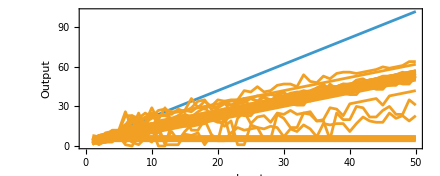

```mathematica
ListLinePlot[Join[{Table[ 2i+2, {i, 50}]}, Length/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0},{{{60}}}], {i, 50}]&/@ dubevosk4[[All, -1]]], PlotHighlighting->None, PlotStyle->Prepend[Table[ColorData["DefaultPlotColors"][2], 60], ColorData["DefaultPlotColors"][1]], Frame->True, FrameLabel->{"Input", "Output"}, AspectRatio->.4]
```

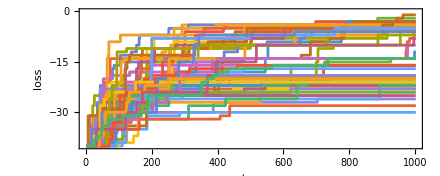

```mathematica
ListStepPlot[#[[All, "Fitness"]]&/@ dubevosk4, Frame->True, FrameLabel->{"steps", "loss"}, AspectRatio->.4]
```

#### All Runs

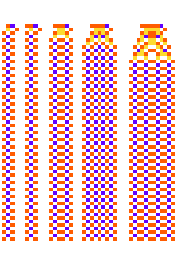
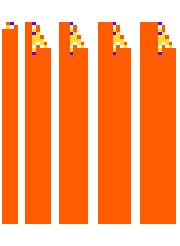
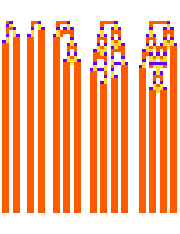
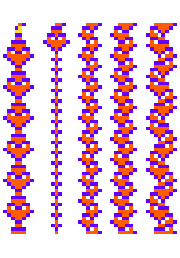
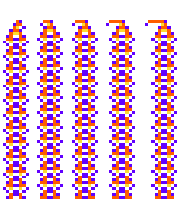
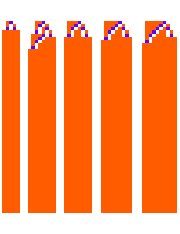
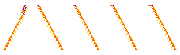
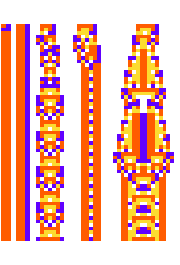

```mathematica
GraphicsRow[ArrayPlot[#, ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]}]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0}, 60], {i, 5}], ImageSize->Small]&[#[[-1]]]&/@ dubevosk4
```

#### k = 3

Just by width of output this one is very close

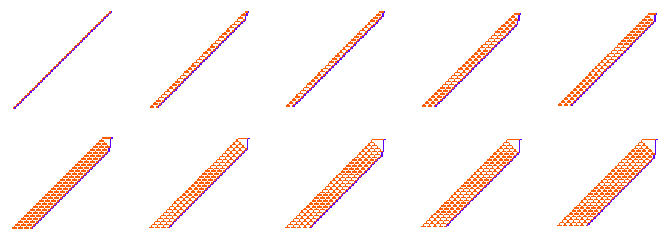

```mathematica
GraphicsGrid[Partition[ArrayPlot[ArrayPad[#, 1]&/@#, ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]}]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0}, 60], {i, 10}]&[dubevosk3[[22, -1]]], 5]]
```

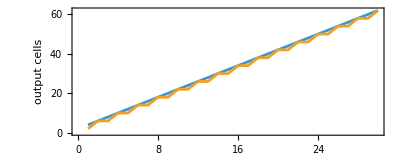

```mathematica
ListLinePlot[Join[{Table[ 2i+2, {i, 30}]}, Length/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0},{{{60}}}], {i, 30}]&/@ {dubevosk3[[22, -1]]}], PlotHighlighting->None, PlotStyle->Prepend[Table[ColorData["DefaultPlotColors"][2], 60], ColorData["DefaultPlotColors"][1]], Frame->True, FrameLabel->{"input cells", "output cells"}, AspectRatio->.4]
```

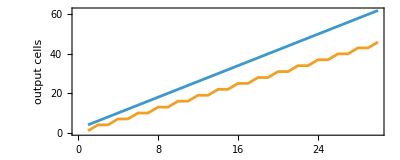

```mathematica
ListLinePlot[Join[{Table[ 2i+2, {i, 30}]}, Count[#, 1]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0},{{{60}}}], {i, 30}]&/@ {dubevosk3[[22, -1]]}], PlotHighlighting->None, PlotStyle->Prepend[Table[ColorData["DefaultPlotColors"][2], 60], ColorData["DefaultPlotColors"][1]], Frame->True, FrameLabel->{"input cells", "output cells"}, AspectRatio->.4]
```

This is the closest by measured fitness

```mathematica
PositionLargest[dubevosk3[[All, "Fitness"]]]
```

Part::pspec1: Part specification Fitness is not applicable.

PositionLargest::rvec2: Input {{{<|Rule -> {0, 3, 1}, Fitness -> -40|>, <<1000>>}, <<59>>}, All, Fitness} is not a real-valued vector.

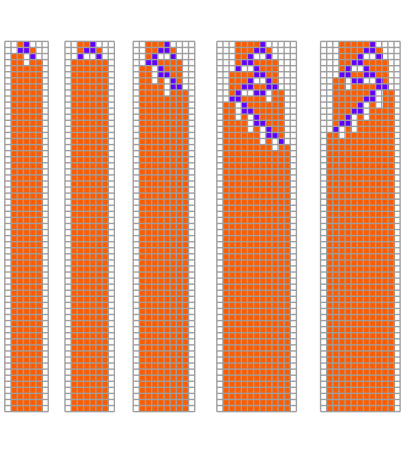

```mathematica
GraphicsRow[ArrayPlot[ArrayPad[#, 1]&/@#, ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]}, Mesh->True]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0}, 60], {i, 5}]&[MaximalBy[dubevosk3, #[[-1, "Fitness"]]&, 1][[1, -1]]]]
```

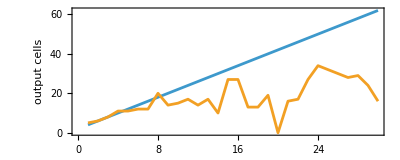

```mathematica
ListLinePlot[Join[{Table[ 2i+2, {i, 30}]}, Count[#, 1]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0},{{{60}}}], {i, 30}]&/@ {MaximalBy[dubevosk3, #[[-1, "Fitness"]]&, 1][[1, -1]]}], PlotHighlighting->None, PlotStyle->Prepend[Table[ColorData["DefaultPlotColors"][2], 60], ColorData["DefaultPlotColors"][1]], Frame->True, FrameLabel->{"input cells", "output cells"}, AspectRatio->.4]
```

All results:

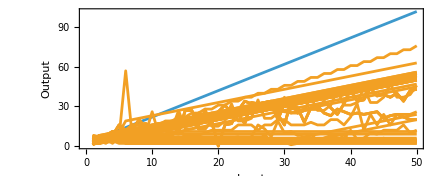

```mathematica
ListLinePlot[Join[{Table[ 2i+2, {i, 50}]}, Count[#, 1]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0},{{{60}}}], {i, 50}]&/@ dubevosk3[[All, -1]]], PlotHighlighting->None, PlotStyle->Prepend[Table[ColorData["DefaultPlotColors"][2], 60], ColorData["DefaultPlotColors"][1]], Frame->True, FrameLabel->{"Input", "Output"}, AspectRatio->.4]
```

```mathematica
dubevosk3 = ParallelTable[
SeedRandom[444210 + j];
AdaptiveCellularAutomaton[<|"Rule"->{0, 3, 1}, "Depth"->1000, 
"MutationFunction"->(RandomRuleMutation[#Rule, 1, "Symmetric"->True]&),
 "FitnessFunction"-> (-Total[Abs[Table[CenterArray[#, Max[Length[#],2i+2]&[#]] - CenterArray[Table[1, 2i+2], Max[Length[#],2i+2]]&[CellularAutomaton[#1, {Append[Table[1, i], 2], 0}, {{{60}}}]] , {i, 5}]], 2]&)|>], {j, 60}];
```

```mathematica
ListStepPlot[#[[All, "Fitness"]]&/@ dubevosk4, Frame->True, FrameLabel->{"steps", "loss"}, AspectRatio->.4]
```

-Graphics-

#### Old k = 4

```mathematica
dubevosk4 = ParallelTable[
SeedRandom[444210 + j];
AdaptiveEvolution[{0, 4, 1}, 1000,
"MutationFunction"->(RandomRuleMutation[#, 1, "Symmetric"->True]&),
 "FitnessFunction"-> (-Total[Abs[Table[CenterArray[#, Max[Length[#],2i+2]&[#]] - CenterArray[Table[1, 2i+2], Max[Length[#],2i+2]]&[CellularAutomaton[#, {Append[Table[1, i], 2], 0}, {{{60}}}]] , {i, 5}]], 2]&)], {j, 30}];
```

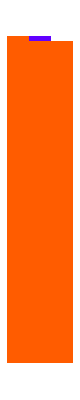
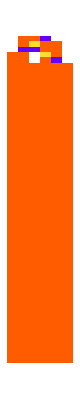
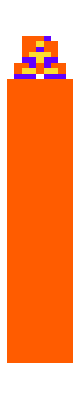
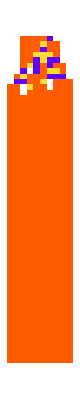
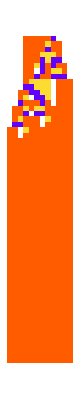

```mathematica
ArrayPlot[#, ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]}]&/@Table[CellularAutomaton[#rule,{Append[Table[1, i], 2], 0}, 60], {i, 5}]&[bestk4[[-1]]]
```

For more inputs

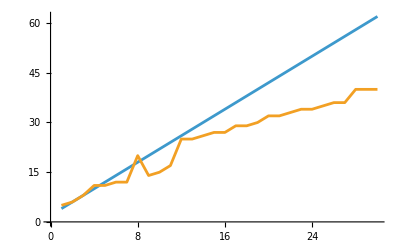

```mathematica
ListLinePlot[Join[{Table[ 2i+2, {i, 30}]}, Length/@Table[CellularAutomaton[#rule,{Append[Table[1, i], 2], 0},{{{60}}}], {i, 30}]&/@ {best[[-1]]}], PlotHighlighting->None, PlotStyle->Prepend[Table[ColorData["DefaultPlotColors"][2], 60], ColorData["DefaultPlotColors"][1]]]
```

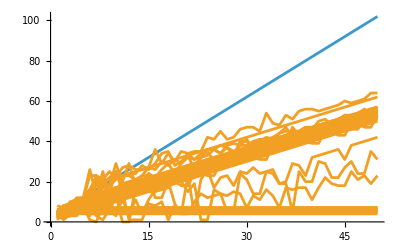

```mathematica
ListLinePlot[Join[{Table[ 2i+2, {i, 50}]}, Length/@Table[CellularAutomaton[#rule,{Append[Table[1, i], 2], 0},{{{60}}}], {i, 50}]&/@ dubevosk4[[All, -1]]], PlotHighlighting->None, PlotStyle->Prepend[Table[ColorData["DefaultPlotColors"][2], 60], ColorData["DefaultPlotColors"][1]]]
```

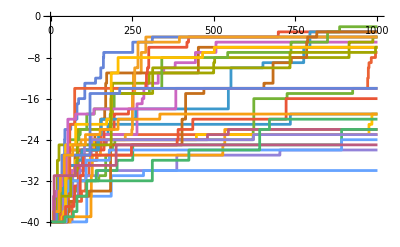

```mathematica
ListStepPlot[#[[All, "fitness"]]&/@ dubevosk4]
```

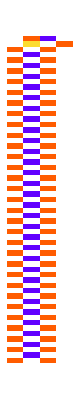
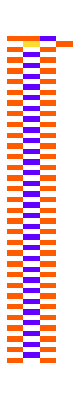
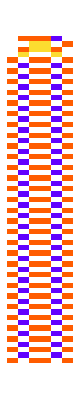
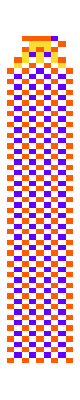
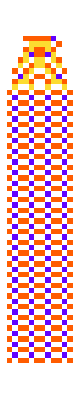
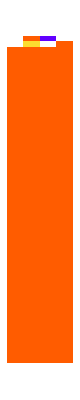
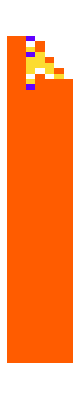
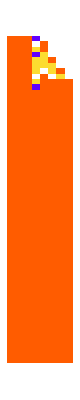
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
ArrayPlot[#, ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]}]&/@Table[CellularAutomaton[#rule,{Append[Table[1, i], 2], 0}, 60], {i, 5}]&[#[[-1]]]&/@ dubevosk4
```

#### Old k = 3

```mathematica
dubevos3 = ParallelTable[
SeedRandom[444310 + j];
AdaptiveEvolution[{0, 3, 1}, 1000,
"MutationFunction"->(RandomRuleMutation[#, 1, "Symmetric"->True]&),
 "FitnessFunction"-> (-Total[Abs[Table[CenterArray[#, Max[Length[#],2i+2]&[#]] - CenterArray[Table[1, 2i+2], Max[Length[#],2i+2]]&[CellularAutomaton[#, {Append[Table[1, i], 2], 0}, {{{60}}}]] , {i, 5}]], 2]&)], {j, 60}];
```

```mathematica
best = First[MaximalBy[dubevos3, #[[-1, "fitness"]]&, 1]];
```

```mathematica
ArrayPlot[#, ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]}]&/@Table[CellularAutomaton[#rule,{Append[Table[1, i], 2], 0}, 60], {i, 5}]&[best[[-1]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListLinePlot[{Table[ 2i+2, {i, 50}], Length/@Table[CellularAutomaton[#rule,{Append[Table[1, i], 2], 0},{{{60}}}], {i, 50}]&[best[[-1]]]}]
```

-Graphics-

```mathematica
ListLinePlot[Join[{Table[ 2i+2, {i, 50}]}, Length/@Table[CellularAutomaton[#rule,{Append[Table[1, i], 2], 0},{{{60}}}], {i, 50}]&/@ dubevos3[[All, -1]]], PlotHighlighting->None, PlotStyle->Prepend[Table[ColorData["DefaultPlotColors"][2], 60], ColorData["DefaultPlotColors"]]]
```

-Graphics-

```mathematica
ListStepPlot[#[[All, "fitness"]]&/@ dubevos3]
```

-Graphics-

### Other fitness functions for complex behavior: longer period

```mathematica
lpevos2 = 
ParallelTable[
SeedRandom[222340  + i];
AdaptiveCellularAutomaton[<|"Rule"->{256, 4, 1}, "Depth"->2000,
"MutationFunction"->(RandomRuleMutation[#Rule, 1, "Symmetric"->True]&),"Cut"->500,
"FitnessFunction"-> (If[# == 201, -Infinity,#]&[LengthWhile[Rest[CellularAutomaton[#1, {{1}, 0}, 200]], Total[#]!=1&] + 1]&)|>, "Final"], {i, 40}];
```

```mathematica
GraphicsGrid[Partition[ArrayPlot[CellularAutomaton[#Rule, {{1}, 0}, 500], ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]}]&/@ lpevos2,20]]
```

-Graphics-

#### Evolution histories

```mathematica
lpevos = 
ParallelTable[
SeedRandom[222210  + i];
AdaptiveCellularAutomaton[<|"Rule"->{256, 4, 1}, "Depth"->1000,
"MutationFunction"->(RandomRuleMutation[#Rule, 1, "Symmetric"->True]&),
 "FitnessFunction"-> (If[# == 201, -Infinity,#]&[LengthWhile[Rest[CellularAutomaton[#1, {{1}, 0}, 200]], #=!=CenterArray[1, Length[#]]&] + 1]&)|>], {i, 10}];
```

```mathematica
GraphicsRow[ArrayPlot[CellularAutomaton[#Rule, {{1}, 0}, 200], ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]}]&/@ GatherBy[#, Last][[All, 1]]]&/@ lpevos
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Larger number of colored cells

#### Asymmetric

```mathematica
evoarea = ParallelTable[
SeedRandom[444210 + j];
AdaptiveCellularAutomaton[<|"Rule"->{0, 3, 1}, "Depth"->1000, 
 "FitnessFunction"-> (
With[{ca = CellularAutomaton[#1, #2, 200]},
If[Total[ca[[-1]]]!= 0, -Infinity, 
Count[ca, x_/;x>0, {2}]]]&)|>], {j, 60}];
```

```mathematica
ListStepPlot[#[[All, "Fitness"]]&/@ evoarea, Frame->True, FrameLabel->{"steps", "fitness"}, AspectRatio->.4, PlotRange->All]
```

-Graphics-

```mathematica
Labeled[ArrayPlot[CellularAutomaton[#Rule, {{1}, 0}, 200], ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]}], #Fitness]&/@ReverseSortBy[evoarea[[All, -1]], #Fitness&]
```

{-Graphics-2027,-Graphics-1211,-Graphics-1134,-Graphics-741,-Graphics-723,-Graphics-721,-Graphics-680,-Graphics-572,-Graphics-551,-Graphics-516,-Graphics-472,-Graphics-442,-Graphics-420,-Graphics-405,-Graphics-359,-Graphics-339,-Graphics-338,-Graphics-333,-Graphics-332,-Graphics-305,-Graphics-273,-Graphics-252,-Graphics-250,-Graphics-228,-Graphics-217,-Graphics-184,-Graphics-159,-Graphics-157,-Graphics-148,-Graphics-133,-Graphics-132,-Graphics-129,-Graphics-120,-Graphics-113,-Graphics-102,-Graphics-102,-Graphics-102,-Graphics-100,-Graphics-94,-Graphics-89,-Graphics-77,-Graphics-72,-Graphics-70,-Graphics-66,-Graphics-47,-Graphics-44,-Graphics-38,-Graphics-31,-Graphics-29,-Graphics-25,-Graphics-12,-Graphics-12,-Graphics-5,-Graphics-5,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1,-Graphics-1}

#### Symmetric version

```mathematica
evoareasym = ParallelTable[
SeedRandom[444210 + j];
AdaptiveCellularAutomaton[<|"Rule"->{0, 3, 1}, "Depth"->1000, 
"MutationFunction"-> (RandomRuleMutation[#Rule, 1, "Symmetric"->True]&),
 "FitnessFunction"-> (
With[{ca = CellularAutomaton[#1, #2, 200]},
If[Total[ca[[-1]]]!= 0, -Infinity, 
Count[ca, x_/;x>0, {2}]]]&)|>], {j, 60}];
```

```mathematica
Labeled[ArrayPlot[CellularAutomaton[#Rule, {{1}, 0}, 200], ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]}], #Fitness]&/@ReverseSortBy[evoareasym[[All, -1]], #Fitness&]
```

{-Graphics-4072,-Graphics-1535,-Graphics-1424,-Graphics-1134,-Graphics-1111,-Graphics-1094,-Graphics-897,-Graphics-857,-Graphics-832,-Graphics-539,-Graphics-509,-Graphics-399,-Graphics-397,-Graphics-378,-Graphics-341,-Graphics-339,-Graphics-335,-Graphics-335,-Graphics-335,-Graphics-333,-Graphics-291,-Graphics-276,-Graphics-275,-Graphics-269,-Graphics-253,-Graphics-240,-Graphics-231,-Graphics-216,-Graphics-207,-Graphics-203,-Graphics-200,-Graphics-167,-Graphics-163,-Graphics-159,-Graphics-142,-Graphics-142,-Graphics-141,-Graphics-139,-Graphics-136,-Graphics-124,-Graphics-113,-Graphics-113,-Graphics-109,-Graphics-102,-Graphics-99,-Graphics-98,-Graphics-96,-Graphics-96,-Graphics-96,-Graphics-92,-Graphics-82,-Graphics-82,-Graphics-81,-Graphics-80,-Graphics-80,-Graphics-75,-Graphics-74,-Graphics-73,-Graphics-60,-Graphics-28}

### Larger bounding area

```mathematica
evoarea2 = ParallelTable[
SeedRandom[444210 + j];
AdaptiveCellularAutomaton[<|"Rule"->{0, 3, 1}, "Depth"->1000, 
 "FitnessFunction"-> (
With[{ca = CellularAutomaton[#1, #2, 200]},
If[Total[ca[[-1]]]!= 0, -Infinity, 
Area[CAPolygon[ca]]/.Undefined->0]]&)|>], {j, 5}];
```

```mathematica
Labeled[ArrayPlot[CellularAutomaton[#Rule, {{1}, 0}, 200], ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]}], #Fitness]&/@ReverseSortBy[evoarea2[[All, -1]], #Fitness&]
```

{-Graphics-2399,-Graphics-2139/2,-Graphics-1006,-Graphics-441/2,-Graphics-133}

### Evolving to a specific sequence

#### s = 4

```mathematica
ArrayPlot[CellularAutomaton[{209218, 2, 2}, {{1}, 0}, {50, {-15, 15}}], Mesh->True]
```

-Graphics-

```mathematica
s = 4;
seq = Catenate[Table[Prepend[Table[0, s], 1], 10]];
evoseq = 
ParallelTable[
SeedRandom[444220 + j];
AdaptiveCellularAutomaton[<|"Rule"->{0, 2, 2}, "Depth"->1000, 
 "FitnessFunction"-> 
(-Total[Abs[Catenate[CellularAutomaton[#1, #2, {Length[seq] - 1, {0}}]] - seq]]&)|>], {j, 100}];
```

Two successful out of 100:

```mathematica
Table[SeedRandom[444220 + j];
GraphicsRow[AdaptiveCellularAutomaton[<|"Rule"->{0, 2, 2}, "Depth"->1000, 
 "FitnessFunction"-> 
(-Total[Abs[Catenate[CellularAutomaton[#1, #2, {Length[seq] - 1, {0}}]] - seq]]&)|>, "Breakthroughs", "Plot"->{50, Automatic}]], {j,Select[evoseq, Last[#]["Fitness"]==0&->"Index"]}]
```

{-Graphics-,-Graphics-}

```mathematica
GraphicsColumn[Table[SeedRandom[444220 + j];
Show[ListStepPlot[#Fitness&/@ #], ListPlot[#MutatedFitness&/@ #, PlotStyle->Red]]&[AdaptiveCellularAutomaton[<|"Rule"->{0, 2, 2}, "Depth"->1000, 
 "FitnessFunction"-> 
(-Total[Abs[Catenate[CellularAutomaton[#1, #2, {Length[seq] - 1, {0}}]] - seq]]&)|>, "All", {"Fitness", "MutatedFitness"}]], {j,Select[evoseq, Last[#]["Fitness"]==0&->"Index"]}] ]
```

-Graphics-

All plots:

```mathematica
ListStepPlot[#[[All, "Fitness"]]&/@ evoseq, Frame->True, FrameLabel->{"steps", "loss"}, AspectRatio->.4]
```

-Graphics-

All finals:

```mathematica
Labeled[ArrayPlot[CellularAutomaton[#Rule, {{1}, 0}, 50], ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->
Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]}], #Fitness]&/@ReverseSortBy[evoseq[[All, -1]], #Fitness&]
```

{-Graphics-0,-Graphics-0,-Graphics--7,-Graphics--7,-Graphics--8,-Graphics--8,-Graphics--8,-Graphics--8,-Graphics--8,-Graphics--8,-Graphics--8,-Graphics--8,-Graphics--8,-Graphics--8,-Graphics--8,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9,-Graphics--9}

#### s = 5

```mathematica
s = 5;
seq5 = Catenate[Table[Prepend[Table[0, s], 1], 9]];
evoseq5 = 
ParallelTable[
SeedRandom[444220 + j];
AdaptiveCellularAutomaton[<|"Rule"->{0, 2, 2}, "Depth"->1000, 
 "FitnessFunction"-> 
(-Total[Abs[Catenate[CellularAutomaton[#1, #2, {Length[seq5] - 1, {0}}]] - seq5]]&)|>], {j, 100}];
```

```mathematica
ListStepPlot[#[[All, "Fitness"]]&/@ evoseq5, Frame->True, FrameLabel->{"steps", "loss"}, AspectRatio->.4, PlotRange->All]
```

-Graphics-

```mathematica
Table[SeedRandom[444220 + j];
GraphicsRow[AdaptiveCellularAutomaton[<|"Rule"->{0, 2, 2}, "Depth"->1000, 
 "FitnessFunction"-> 
(-Total[Abs[Catenate[CellularAutomaton[#1, #2, {Length[seq5] - 1, {0}}]] - seq5]]&)|>, "Breakthroughs", "Plot"->{50, Automatic}]], {j,Select[evoseq5, Last[#]["Fitness"]==-2&->"Index"]}]
```

{-Graphics-}

#### s = 6

```mathematica
s = 6;
seq6 = Catenate[Table[Prepend[Table[0, s], 1], 9]];
evoseq6 = 
ParallelTable[
SeedRandom[444220 + j];
AdaptiveCellularAutomaton[<|"Rule"->{0, 2, 2}, "Depth"->1000, 
 "FitnessFunction"-> 
(-Total[Abs[Catenate[CellularAutomaton[#1, #2, {Length[seq6] - 1, {0}}]] - seq6]]&)|>], {j, 100}];
```

```mathematica
ListStepPlot[#[[All, "Fitness"]]&/@ evoseq6, Frame->True, FrameLabel->{"steps", "loss"}, AspectRatio->.4, PlotRange->All]
```

-Graphics-

```mathematica
Table[SeedRandom[444220 + j];
GraphicsRow[AdaptiveCellularAutomaton[<|"Rule"->{0, 2, 2}, "Depth"->1000, 
 "FitnessFunction"-> 
(-Total[Abs[Catenate[CellularAutomaton[#1, #2, {Length[seq6] - 1, {0}}]] - seq6]]&)|>, "Breakthroughs", "Plot"->{50, Automatic}]], {j,Select[evoseq6, Last[#]["Fitness"]==0&->"Index"]}]
```

{}

#### allseqs

5 best from 100 evolutions for each sequence. Only s = 9 successfully found one but s = 4  and s = 5 were only one off. I bet that if we run the longer sequences with a longer cut results will be better

```mathematica
Module[{seq}, 
allseqs = Table[
seq  = Catenate[Table[Prepend[Table[0, s], 1], Ceiling[50 / (s + 1)]]];
ParallelTable[
SeedRandom[547220 + j];
AdaptiveCellularAutomaton[<|"Rule"->{0, 2, 2}, "Depth"->1000, 
 "FitnessFunction"-> 
(-Total[Abs[Catenate[CellularAutomaton[#1, #2, {Length[seq] - 1 , {0}}]] - seq]]&)|>, "Final"], {j, 100}],
{s, 4, 23}]];
```

```mathematica
Iconize[allseqs]
```

```mathematica
ByteCount[allseqs]
```

1057480

```mathematica
MapIndexed[Labeled[GraphicsRow[Labeled[ArrayPlot[CellularAutomaton[#Rule, {{1}, 0}, 55]], Text[#Fitness]]&/@ TakeLargestBy[#, #Fitness&,5], Frame->True], "s = "<>ToString[First[#2]+3]]&, allseqs]
```

{-Graphics-s = 4,-Graphics-s = 5,-Graphics-s = 6,-Graphics-s = 7,-Graphics-s = 8,-Graphics-s = 9,-Graphics-s = 10,-Graphics-s = 11,-Graphics-s = 12,-Graphics-s = 13,-Graphics-s = 14,-Graphics-s = 15,-Graphics-s = 16,-Graphics-s = 17,-Graphics-s = 18,-Graphics-s = 19,-Graphics-s = 20,-Graphics-s = 21,-Graphics-s = 22,-Graphics-s = 23}

### Closer look at patch distributions

#### Most frequent

```mathematica
Table[With[{ca =CellularAutomaton[k5evos[[i, 1]], {{1}, 0}, k5evos[[i, 2]] + 1]},  GraphicsRow[{ArrayPatchFrequencyChart[ca, {3, 3}, {1, 1},{2, UpTo[40]}, "ShowSequences"->True,"SequenceSize"->{12, 12}, ImageSize->{100, Automatic}],ArrayPlot[ca, ColorRules->colorrules, ImageSize->{100, Automatic}]}]], {i, {8, 16, 27}}]
```

{-Graphics-,-Graphics-,-Graphics-}

#### Whole distribution

```mathematica
Table[With[{ca =CellularAutomaton[k5evos[[i, 1]], {{1}, 0}, k5evos[[i, 2]] + 1]}, 
Length[Counts[Catenate[Partition[ca, {3, 3}, {1, 1}]]]]], {i, {8, 16, 27}}]
```

{1426,6143,11563}

```mathematica
Table[With[{ca =CellularAutomaton[k5evos[[i, 1]], {{1}, 0}, k5evos[[i, 2]] + 1]},  GraphicsRow[{ListStepPlot[Rest[Values[ReverseSort[Counts[Catenate[Partition[ca, {3, 3}, {1, 1}]]]]]], ImageSize->{100, Automatic}, ScalingFunctions->"Log", PlotRange->{{0, 12000},Automatic}],ArrayPlot[ca, ColorRules->colorrules, ImageSize->{100, Automatic}]}]], {i, {8, 16, 27}}]
```

{-Graphics-,-Graphics-,-Graphics-}

#### Distributions of many

```mathematica
ListPlot3D[Catenate[MapIndexed[Append[Reverse[#2], #1]&, SortBy[Values[Rest[ReverseSort[Counts[Catenate[Partition[CellularAutomaton[#[[1]], {{1}, 0}, 200],{3, 3}, {1, 1}]]]]]]&/@ Select[k5evos, Last[#] >100&], Entropy], {2}] ]]
```

-Graphics3D-

#### TODO: See how this changes with different block sizes

### TODO: Information Propagation